```mathematica
ϵ=0.002
```

0.002

```mathematica
k=8.617*10^-5
```

0.00008617

```mathematica
V=0.01
```

0.01

```mathematica
T=1
```

1

```mathematica
xmax=k T-ϵ+V
```

-0.00346915

```mathematica
f[ V+2 ϵ]
```

8.95432×10^-7

```mathematica
f[x_]:=  (x+ϵ)/(√((x+2 ϵ) x))(1/(Exp[(x+ϵ-V)/(k T)]+1)-1/(Exp[(x+ϵ+V)/(k T)]+1))
```

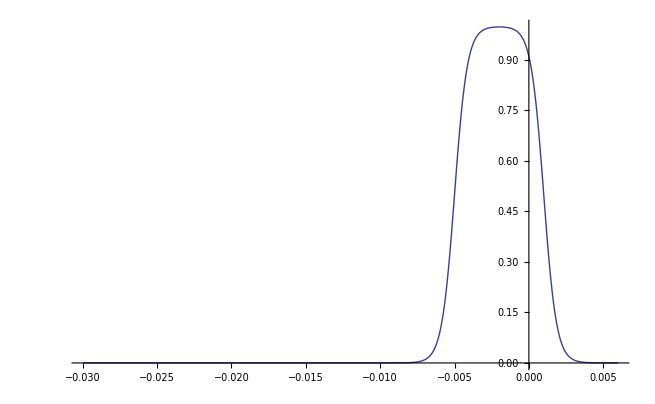

```mathematica
Plot[f[x],{x,-10 V,2 V}]
```

```mathematica
NSolve[f[x]==0.01,x]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

NSolve[((1/(1+ⅇ^(2320.99 (-0.01+x)))-1/(1+ⅇ^(2320.99 (0.05+x)))) (0.02+x))/(√(x (0.04+x)))==0.01,x]

```mathematica
Series[(1/(Exp[(x+ϵa-Va)/(ka Ta)]+1)-1/(Exp[(x+ϵa+Va)/(ka Ta)]+1)),{x,0,1}]
```

(1/(1+ⅇ^(-Va/(ka Ta)+ϵa/(ka Ta)))-1/(1+ⅇ^(Va/(ka Ta)+ϵa/(ka Ta))))+(-ⅇ^(-Va/(ka Ta)+ϵa/(ka Ta))/((1+ⅇ^(-Va/(ka Ta)+ϵa/(ka Ta)))^2 ka Ta)+ⅇ^(Va/(ka Ta)+ϵa/(ka Ta))/((1+ⅇ^(Va/(ka Ta)+ϵa/(ka Ta)))^2 ka Ta)) x+O[x]^2

```mathematica
Integrate[ (x+ϵa)/(√((x+2 ϵa) x)),{x,-b,b}]
```

If[Re[ϵa/b]≥1/2||Re[ϵa/b]≤-1/2||Im[ϵa/b]≠0,-√(b (b-2 ϵa))+√(b (b+2 ϵa)),Integrate[(x+ϵa)/(√(x (x+2 ϵa))),{x,-b,b},Assumptions→!(Re[ϵa/b]≥1/2||Re[ϵa/b]≤-1/2||Im[ϵa/b]≠0)]]

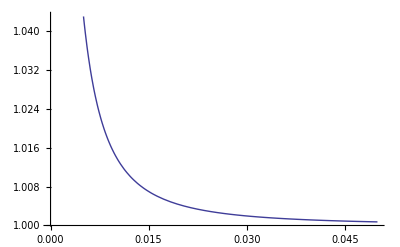

```mathematica
Plot[ (x+ϵ)/(√((x+2 ϵ) x)),{x,0,0.05}]
```

```mathematica
ⅇ^(-V/(k T)+ϵ/(k T))/((1+ⅇ^(-V/(k T)+ϵ/(k T)))^2 k T)+ⅇ^(V/(k T)+ϵ/(k T))/((1+ⅇ^(V/(k T)+ϵ/(k T)))^2 k T)
```

191.137

```mathematica
fermidiff[x_]:= (1/(Exp[(x+ϵ-V)/(k T)]+1)-1/(Exp[(x+ϵ+V)/(k T)]+1))
```

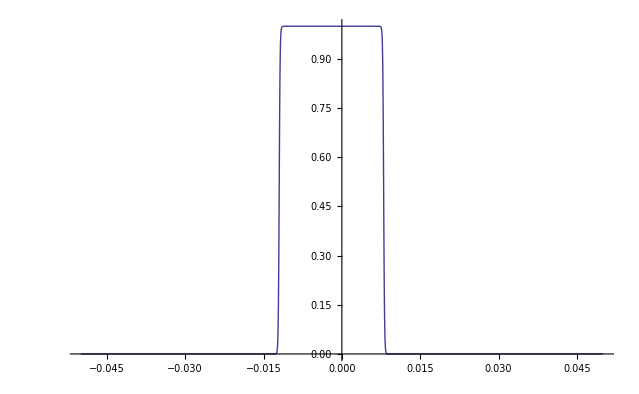

```mathematica
Plot[ fermidiff[x],{x,-0.05,0.05}]
```

```mathematica
fermi_diff[0]
```

fermi_diff[0]

```mathematica
Series[Integrate[(x+ϵ)/(√((x+2 ϵ) x)),x],{x,0,3}]
```

√2 √ϵ √x+x^(3/2)/(2 √2 √ϵ)-x^(5/2)/(16 (√2 ϵ^(3/2)))+O[x]^(7/2)